```mathematica
ω=2000 ;
c1=-ζ ω+ω √(ζ^2-1);
c2=-ζ ω-ω √(ζ^2-1);
H=ω^2/((s-c1)(s-c2));
```

```mathematica
ζ=0.25
```

0.25

```mathematica
tfm=TransferFunctionModel[ω^2/(s^2+2*ζ*ω*s+ω^2),s]
```

4000000/(4000000+1000. s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11400000040000001FalseFalseFalseAutomaticNoneAutomatic

```mathematica
StepResponse=OutputResponse[tfm,UnitStep[t],t];
```

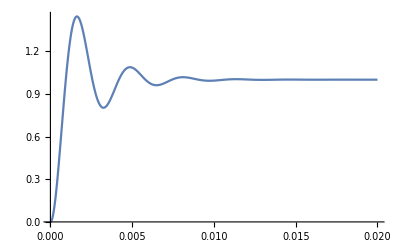

```mathematica
Plot[StepResponse,{t,0,0.02},PlotRange->All]
```

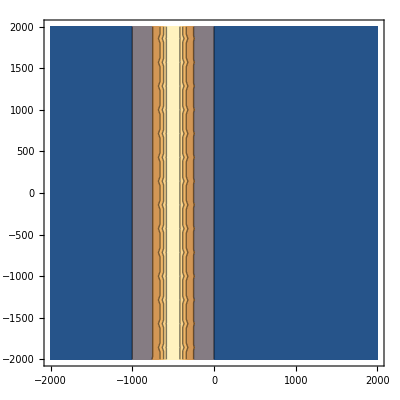
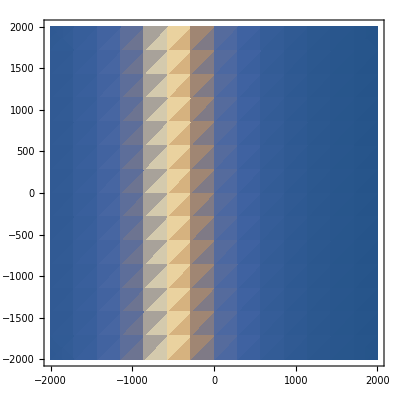
{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
Block[{s=σ+I ω},Table[plot[Abs[H],{σ,-2000,2000},{ω,-2000,2000},PlotRange->All],{plot,{Plot3D,ContourPlot,DensityPlot}}]]
```